```mathematica
cellvideo = "/home/tom/complex/MP2/Gifs/jbc.M112.437913-21.gif";
```

```mathematica
frames = Import[cellvideo];
```

```mathematica
a=frames[[2]];
```

```mathematica
dims=ImageDimensions[frames⟦2⟧]
splitChannels=Flatten[Map[(ImagePartition[#, {dims⟦1⟧/2,dims⟦2⟧}])&, frames],1];
b = splitChannels[[2]];
Export["/home/tom/complex/MP2/EndOfWeek2/rawsampleframe.png",GraphicsGrid[{{a}},ImageSize->800],"PNG"]
Export["/home/tom/complex/MP2/EndOfWeek2/splitampleframe.png",GraphicsGrid[{b},ImageSize->800],"PNG"]
```

{1024,512}

/home/tom/complex/MP2/EndOfWeek2/rawsampleframe.png

/home/tom/complex/MP2/EndOfWeek2/splitampleframe.png

```mathematica
(*averageImage=Image[Mean[Map[ImageData[#]&,splitChannels⟦All,1⟧]]] *)
```

```mathematica
(*x = ImageData[splitChannels[[1]]]
Image[Mean[x]]*)
averageImage=Image[Mean[Map[ImageData[#]&,splitChannels⟦All,1⟧]]]
```

-Graphics-

```mathematica
detectedCells = MorphologicalComponents[averageImage,0.07];
cleanDetectedCells = SelectComponents[detectedCells,(#Area > 100) &];
Colorize[detectedCells]
Colorize[cleanDetectedCells]
Length[detectedCells[[1]]]
```

-Graphics-

-Graphics-

512

```mathematica
Export["/home/tom/complex/MP2/EndOfWeek2/morphcomp.png",GraphicsGrid[{{averageImage,Colorize[detectedCells],Colorize[cleanDetectedCells]},{"(a)","(b)","(c)"}},ImageSize->1000,Alignment->{Center,Top}],"PNG"]
```

/home/tom/complex/MP2/EndOfWeek2/morphcomp.png

```mathematica
cells=ComponentMeasurements[cleanDetectedCells,{"Centroid","SemiAxes","Orientation"}];
```

```mathematica
labels= Flatten[Table[{Yellow, Text[cells⟦i,1⟧, cells⟦i,2,1⟧]}, {i, Length[cells]}]];
GraphicsRow[{ImageCompose[HighlightImage[averageImage,Colorize[cleanDetectedCells]],Graphics[labels]]},ImageSize->400]
```

-Graphics-

```mathematica
cells;
```

```mathematica
boundingEllipses = Map[Rotate[Disk[#[[1]],#[[2]]],#[[3]]]&,Table[{cells[[i]][[2]][[1]],cells[[i]][[2]][[2]],cells[[i]][[2]][[3]]},{i, Length[cells]}]];
labels= Flatten[Table[{Yellow, Text[cells⟦i,1⟧, cells⟦i,2,1⟧]}, {i, Length[cells]}]];

ImageCompose[HighlightImage[averageImage,boundingEllipses],Graphics[labels]]
Export["/home/tom/complex/MP2/EndOfWeek2/boundingellipses.png",ImageCompose[HighlightImage[averageImage,boundingEllipses],Graphics[labels]], "PNG"]
```

-Graphics-

/home/tom/complex/MP2/EndOfWeek2/boundingellipses.png

```mathematica
cellIntensities = Table[Map[{#[[1]],#[[2]]}&,ComponentMeasurements[{cleanDetectedCells,splitChannels⟦i,1⟧},"MeanIntensity"]],{i,Length[splitChannels]}];
```

```mathematica
mainHeader = {"Cell", "Av. Intensity per frame(time/s)"};
frameTimes = Table[1.1*i,{i,0,Length[frames]-1}];
subHeader = Join[{""},frameTimes];
outData = Table[Join[{Transpose[cellIntensities][[i]][[1]][[1]]},Map[#[[2]]&,Transpose[cellIntensities][[i]]]],{i,Length[cells]}];
results = Join[{mainHeader},{frameTimes},outData];
```

```mathematica
Export["/home/tom/complex/MP2/results/intensities.csv",results,"CSV"]
```

/home/tom/complex/MP2/results/intensities.csv

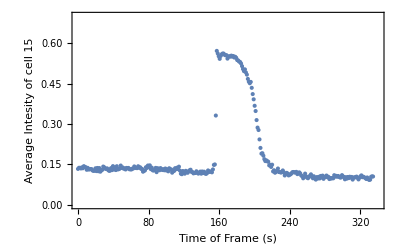

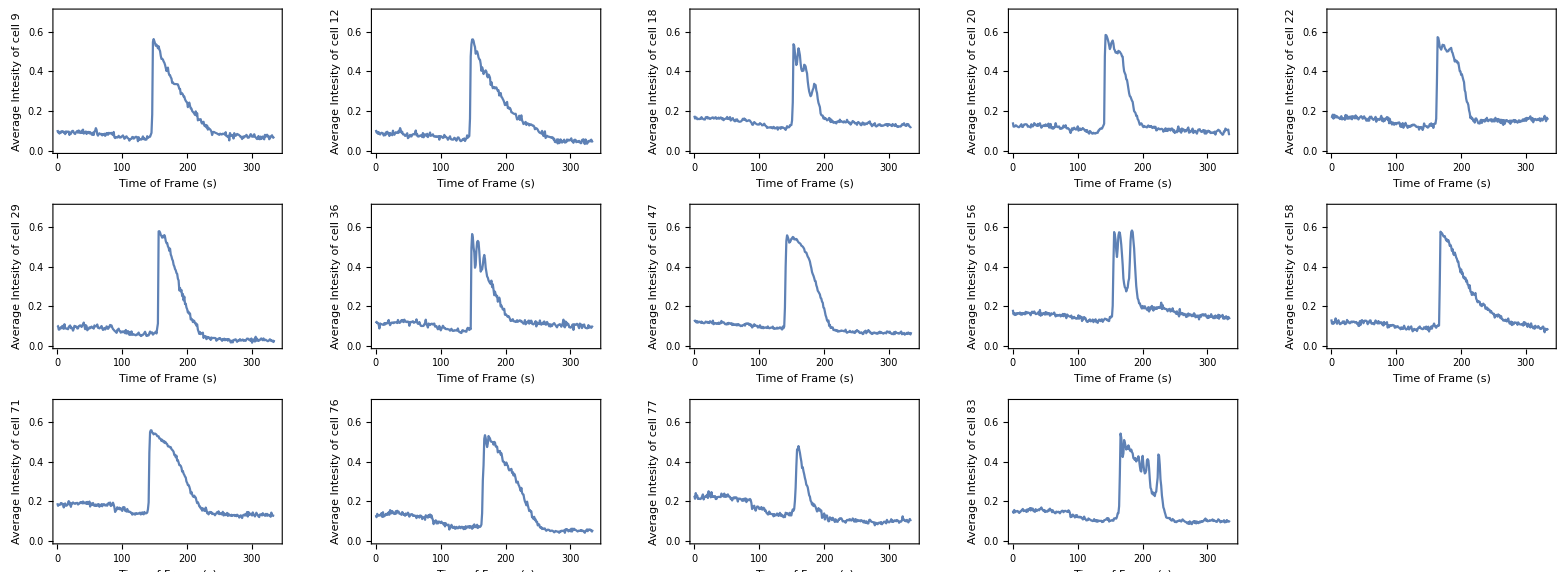

/home/tom/complex/MP2/EndOfWeek2/sampleIntPlots.png

```mathematica
Partition[Riffle[frameTimes,Map[#⟦2⟧&,Transpose[cellIntensities]⟦11⟧]],2];
(* single specific plot *)
ListPlot[Partition[Riffle[frameTimes,Map[#⟦2⟧&,Transpose[cellIntensities]⟦11⟧]],2],PlotRange->{{-0,340},{0,0.7}},Frame-> True,FrameLabel->{"Time of Frame (s)",StringJoin["Average Intesity of cell ",IntegerString[Transpose[cellIntensities]⟦11⟧⟦1⟧⟦1⟧]]}]

(*multiple plots *)
plots = Table[ListLinePlot[Partition[Riffle[frameTimes,Map[#⟦2⟧&,Transpose[cellIntensities]⟦i⟧]],2],PlotRange->{{-0,340},{0,0.7}}, Frame -> True,FrameLabel->{"Time of Frame (s)",StringJoin["Average Intesity of cell ",IntegerString[Transpose[cellIntensities]⟦i⟧⟦1⟧⟦1⟧]]}],{i,{6,9,13,15,16,20,25,30,36,38,46,50,51,55}}];
GraphicsGrid[Partition[plots,UpTo[5]],ImageSize->1600]

Export["/home/tom/complex/MP2/EndOfWeek2/sampleIntPlots.png",GraphicsGrid[Partition[plots,UpTo[5]],ImageSize->1600],"PNG"]
```

{0.,2.2,4.4,6.6,8.8,11.,13.2,15.4,17.6,19.8,22.,24.2,26.4,28.6,30.8,33.,35.2,37.4,39.6,41.8,44.,46.2,48.4,50.6,52.8,55.,57.2,59.4,61.6,63.8,66.,68.2,70.4,72.6,74.8,77.,79.2,81.4,83.6,85.8,88.,90.2,92.4,94.6,96.8,99.,101.2,103.4,105.6,107.8,110.,112.2,114.4,116.6,118.8,121.,123.2,125.4,127.6,129.8,132.,134.2,136.4,138.6,140.8,143.,145.2,147.4,149.6,151.8,154.,156.2,158.4,160.6,162.8,165.,167.2,169.4,171.6,173.8,176.,178.2,180.4,182.6,184.8,187.,189.2,191.4,193.6,195.8,198.,200.2,202.4,204.6,206.8,209.,211.2,213.4,215.6,217.8,220.,222.2,224.4,226.6,228.8,231.,233.2,235.4,237.6,239.8,242.,244.2,246.4,248.6,250.8,253.,255.2,257.4,259.6,261.8,264.,266.2,268.4,270.6,272.8,275.,277.2,279.4,281.6,283.8,286.,288.2,290.4,292.6,294.8,297.,299.2,301.4,303.6,305.8,308.,310.2,312.4,314.6,316.8,319.,321.2,323.4,325.6,327.8}

{512,512}

{512,512}

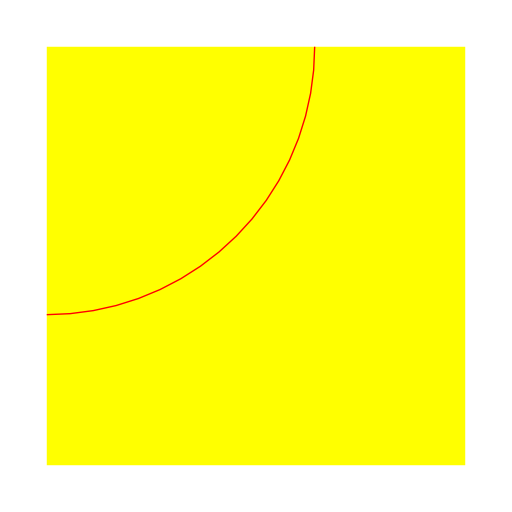

-Graphics-

```mathematica
(*wave modelling*)
phi = 0;
k = 1;
w = 2;
A=1;
B = 1;
(*t = {0,1.1,2.2,3.3,4.4};*)
rzero=0;
radii =Table[(ArcCos[A/B]+w*t - phi)/k,{t,0,149*1.1,1.1}]
circles = Map[{Red,Circle[{0,512},#,{-Pi/2,0}]}&,radii];
concircles = Graphics[circles,ImageSize->{512,512}];
ImageCompose[averageImage,concircles,{0,512}];
ImageDimensions[Graphics[{Yellow,Rectangle[{0,0},{512,512}],circles⟦150⟧},ImageSize->{512,512}]]
ImageDimensions[splitChannels⟦150,1⟧]
Graphics[{Yellow,Rectangle[{0,0},{512,512}],circles⟦150⟧}]
HighlightImage[splitChannels⟦150,1⟧,{circles⟦150⟧},ImageSize->{512,512}]
```

```mathematica
weq2=Laplacian[u[x,y,t],{x,y}]==D[u[x,y,t],{t,2}];

bc2={u[x,Pi,t]==0,u[x,0,t]==0,u[0,y,t]==0,u[Pi,y,t]==0};
ic2={u[x,y,0]==Cos[m x+n y],Derivative[0,0,1][u][x,y,0]==0};
nsol2=NDSolve[{weq2,bc2,ic2}/.{m->1,n->1},u,{x,0,Pi},{y,0,Pi},{t,0,10}];

ListAnimate[Table[Plot3D[u[x,y,t]/.nsol2,{x,0,π},{y,0,π},AxesLabel->Automatic,PlotRange->{{0,π},{0,π},{-1,1}}],{t,0,10}]]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::eerr: Warning: scaled local spatial error estimate of 52.0622 at t = 10. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 15 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
MapIndexed[Flatten[{#2,#⟦2⟧}]&,Transpose[cellIntensities]⟦1⟧];
Length[frameTimes];
Max[Map[#⟦2⟧&,Transpose[cellIntensities][[1]]] ];
Transpose[cellIntensities][[1]];
cellIntensities[[1]][[1]][[1]]
maxIntensities = Table[Flatten[{Transpose[cellIntensities]⟦i⟧⟦1⟧⟦1⟧,Ordering[Transpose[cellIntensities]⟦i⟧,-1]}],{i,Length[Transpose[cellIntensities]]}];
truemaxIntensities = Map[{#⟦1⟧,(#⟦2⟧-1)*1.1}&,maxIntensities]
Transpose[cellIntensities][[1]][[133]];

Select[truemaxIntensities, 140 < #[[2]] < 150 &]
cells[[1]][[2]][[1]]
splitChannels[[130]]
```

2

{{2,145.2},{3,155.1},{5,158.4},{6,167.2},{7,169.4},{9,148.5},{10,168.3},{11,173.8},{12,149.6},{13,158.4},{15,157.3},{17,170.5},{18,152.9},{19,178.2},{20,143.},{22,163.9},{23,143.},{24,151.8},{27,143.},{29,157.3},{32,184.8},{33,147.4},{34,150.7},{35,176.},{36,148.5},{42,151.8},{43,162.8},{44,165.},{45,162.8},{47,143.},{50,160.6},{51,171.6},{52,149.6},{53,162.8},{54,146.3},{56,183.7},{57,187.},{58,168.3},{59,174.9},{60,178.2},{61,151.8},{63,151.8},{64,177.1},{65,144.1},{66,167.2},{71,144.1},{72,173.8},{74,151.8},{75,162.8},{76,168.3},{77,160.6},{78,182.6},{79,162.8},{80,179.3},{83,166.1},{84,160.6},{85,193.6},{86,157.3},{87,166.1},{88,155.1},{89,170.5},{90,146.3},{91,176.},{92,167.2},{93,145.2},{94,146.3},{95,152.9},{96,178.2},{97,158.4},{99,169.4},{100,160.6},{101,150.7},{102,140.8},{103,154.},{105,167.2},{108,169.4},{109,184.8},{110,167.2},{111,170.5},{112,169.4},{113,187.},{114,145.2},{115,158.4},{116,160.6},{117,169.4},{118,191.4},{119,165.},{120,174.9},{121,143.},{122,179.3},{123,187.},{124,180.4},{125,176.},{126,171.6},{127,154.},{129,174.9},{130,191.4},{132,180.4},{135,165.},{136,167.2},{137,187.},{138,200.2},{140,155.1},{141,162.8},{142,196.9},{144,154.},{145,160.6},{147,180.4},{148,195.8},{149,202.4},{150,152.9},{151,170.5},{152,157.3},{153,198.},{154,199.1},{155,188.1},{156,157.3},{157,187.},{158,169.4},{159,152.9},{160,176.},{161,165.},{162,162.8},{163,147.4},{164,195.8},{167,163.9},{168,189.2},{169,179.3},{171,195.8},{172,194.7},{174,193.6},{177,176.},{178,172.7},{180,181.5},{181,196.9},{182,165.},{183,174.9},{185,171.6},{186,158.4},{187,180.4},{189,191.4},{190,191.4},{191,193.6},{192,178.2},{193,173.8},{195,156.2},{196,166.1},{198,178.2},{199,171.6},{200,176.},{202,176.},{203,181.5},{205,204.6},{206,189.2},{207,155.1},{208,187.},{210,167.2},{212,169.4},{213,184.8},{214,151.8},{215,178.2},{216,182.6},{217,158.4},{218,173.8},{219,171.6},{220,169.4},{221,179.3},{222,193.6},{223,169.4},{225,165.},{226,169.4},{227,176.},{228,193.6},{229,198.},{230,159.5},{231,165.},{235,200.2},{237,159.5},{238,160.6},{239,170.5},{240,172.7},{241,180.4}}

{{2,145.2},{9,148.5},{12,149.6},{20,143.},{23,143.},{27,143.},{33,147.4},{36,148.5},{47,143.},{52,149.6},{54,146.3},{65,144.1},{71,144.1},{90,146.3},{93,145.2},{94,146.3},{102,140.8},{114,145.2},{121,143.},{163,147.4}}

{63.25,505.493}

{-Graphics-,-Graphics-}

```mathematica
2
```

{{2,145.2},{3,155.1},{5,158.4},{6,167.2},{7,169.4},{9,148.5},{10,168.3},{11,173.8},{12,149.6},{13,158.4},{15,157.3},{17,170.5},{18,152.9},{19,178.2},{20,143.},{22,163.9},{23,143.},{24,151.8},{27,143.},{29,157.3},{32,184.8},{33,147.4},{34,150.7},{35,176.},{36,148.5},{42,151.8},{43,162.8},{44,165.},{45,162.8},{47,143.},{50,160.6},{51,171.6},{52,149.6},{53,162.8},{54,146.3},{56,183.7},{57,187.},{58,168.3},{59,174.9},{60,178.2},{61,151.8},{63,151.8},{64,177.1},{65,144.1},{66,167.2},{71,144.1},{72,173.8},{74,151.8},{75,162.8},{76,168.3},{77,160.6},{78,182.6},{79,162.8},{80,179.3},{83,166.1},{84,160.6},{85,193.6},{86,157.3},{87,166.1},{88,155.1},{89,170.5},{90,146.3},{91,176.},{92,167.2},{93,145.2},{94,146.3},{95,152.9},{96,178.2},{97,158.4},{99,169.4},{100,160.6},{101,150.7},{102,140.8},{103,154.},{105,167.2},{108,169.4},{109,184.8},{110,167.2},{111,170.5},{112,169.4},{113,187.},{114,145.2},{115,158.4},{116,160.6},{117,169.4},{118,191.4},{119,165.},{120,174.9},{121,143.},{122,179.3},{123,187.},{124,180.4},{125,176.},{126,171.6},{127,154.},{129,174.9},{130,191.4},{132,180.4},{135,165.},{136,167.2},{137,187.},{138,200.2},{140,155.1},{141,162.8},{142,196.9},{144,154.},{145,160.6},{147,180.4},{148,195.8},{149,202.4},{150,152.9},{151,170.5},{152,157.3},{153,198.},{154,199.1},{155,188.1},{156,157.3},{157,187.},{158,169.4},{159,152.9},{160,176.},{161,165.},{162,162.8},{163,147.4},{164,195.8},{167,163.9},{168,189.2},{169,179.3},{171,195.8},{172,194.7},{174,193.6},{177,176.},{178,172.7},{180,181.5},{181,196.9},{182,165.},{183,174.9},{185,171.6},{186,158.4},{187,180.4},{189,191.4},{190,191.4},{191,193.6},{192,178.2},{193,173.8},{195,156.2},{196,166.1},{198,178.2},{199,171.6},{200,176.},{202,176.},{203,181.5},{205,204.6},{206,189.2},{207,155.1},{208,187.},{210,167.2},{212,169.4},{213,184.8},{214,151.8},{215,178.2},{216,182.6},{217,158.4},{218,173.8},{219,171.6},{220,169.4},{221,179.3},{222,193.6},{223,169.4},{225,165.},{226,169.4},{227,176.},{228,193.6},{229,198.},{230,159.5},{231,165.},{235,200.2},{237,159.5},{238,160.6},{239,170.5},{240,172.7},{241,180.4}}

{{2,145.2},{9,148.5},{12,149.6},{20,143.},{23,143.},{27,143.},{33,147.4},{36,148.5},{47,143.},{52,149.6},{54,146.3},{65,144.1},{71,144.1},{90,146.3},{93,145.2},{94,146.3},{102,140.8},{114,145.2},{121,143.},{163,147.4}}

{2→{{63.25,505.493},{8.88541,5.49012},2.49814},3→{{204.971,506.478},{11.4964,7.29816},-2.30309},5→{{262.417,503.409},{8.33477,4.69836},-1.52196},6→{{315.876,501.099},{18.3629,7.82376},2.57278},7→{{371.905,506.605},{12.9764,5.06642},-2.75777},9→{{134.483,498.96},{8.25913,6.76178},-2.22474},10→{{341.99,498.5},{9.04091,6.85969},-0.845443},11→{{469.357,488.295},{19.8586,6.94591},-1.95507},12→{{107.266,498.086},{8.63355,4.78539},-2.11584},13→{{272.079,489.123},{14.7794,5.55125},-1.55244},15→{{215.066,489.68},{12.8284,7.06528},-1.98632},17→{{375.895,487.84},{14.0749,5.02932},-2.17822},18→{{181.739,493.608},{24.4213,6.71981},-0.902375},19→{{437.623,491.284},{8.7694,6.29832},-0.997301},20→{{56.5373,492.214},{10.0305,5.26806},2.48038},22→{{287.372,475.782},{16.0275,4.86062},-1.42047},23→{{32.2149,477.292},{9.2747,7.62095},-1.14949},24→{{96.1255,475.528},{16.7124,5.28899},2.62323},27→{{64.7542,473.285},{11.4334,4.9516},2.3832},29→{{234.638,473.072},{8.16665,5.38169},-0.863842},32→{{437.743,463.58},{20.1801,9.74055},2.78775},33→{{98.4135,456.495},{13.2453,5.14166},-1.23243},34→{{158.28,456.185},{8.11744,7.97601},-1.03678},35→{{400.199,457.418},{9.32198,5.78597},-2.73492},36→{{129.879,453.397},{7.30079,5.29255},-1.19862},42→{{65.1713,444.21},{11.2404,8.21248},-0.908425},43→{{339.957,442.87},{11.9105,4.66649},-1.26824},44→{{264.447,443.132},{10.2461,7.18718},2.676},45→{{360.434,444.123},{8.22338,7.10637},3.04978},47→{{26.7136,439.15},{19.9096,6.85526},2.64625},50→{{182.856,439.281},{21.2274,12.0253},-3.02809},51→{{398.057,438.485},{10.8243,6.15388},-2.64335},52→{{143.325,431.961},{8.62508,5.74894},-1.99348},53→{{286.753,423.93},{15.2713,6.6841},-1.29942},54→{{13.2014,425.599},{14.4056,7.72741},-0.872452},56→{{223.647,415.247},{16.6963,7.22769},-1.81258},57→{{496.996,412.184},{18.8746,8.68022},-1.02056},58→{{372.574,412.217},{11.2494,6.82432},-0.958318},59→{{400.936,404.723},{16.7061,8.70741},-2.13214},60→{{441.655,398.037},{21.463,11.2728},-1.06607},61→{{160.985,405.816},{12.471,7.50266},-1.12939},63→{{134.59,403.18},{14.1774,5.66276},2.51116},64→{{488.767,397.586},{11.7747,5.77472},-1.03345},65→{{87.1429,397.346},{8.41142,7.08855},-1.79353},66→{{251.509,394.027},{8.75208,8.2596},2.60464},71→{{17.0361,382.328},{14.4306,9.59212},-1.46358},72→{{312.257,398.884},{28.6581,18.5392},-0.845801},74→{{83.5563,378.236},{10.3041,7.2858},-3.07077},75→{{135.813,376.196},{13.5138,5.35297},-2.45075},76→{{358.086,373.897},{14.8846,7.60224},-0.802041},77→{{162.791,372.547},{10.1362,6.7196},-2.32363},78→{{472.515,371.096},{8.69386,7.4622},-0.819052},79→{{235.393,367.977},{9.20942,7.39335},-1.23803},80→{{450.289,362.974},{16.7028,5.20844},-1.26664},83→{{330.563,350.275},{13.8849,11.851},-0.887733},84→{{206.666,331.888},{32.0014,13.6731},-1.6162},85→{{498.927,355.704},{8.72796,7.8511},2.58979},86→{{95.0402,352.851},{8.49658,6.66521},2.39664},87→{{281.076,354.956},{19.4526,16.1794},3.05594},88→{{177.64,346.996},{12.5943,6.58475},-1.80259},89→{{307.42,346.557},{10.2315,5.58047},-2.18824},90→{{45.1786,341.036},{8.81165,4.08053},-2.51107},91→{{414.793,321.18},{24.4704,5.91567},2.37914},92→{{442.872,327.6},{14.0818,5.66156},-1.25226},93→{{9.66981,331.16},{7.44625,6.82591},-1.97464},94→{{63.1527,330.122},{13.9846,9.21229},3.04},95→{{92.0779,327.203},{10.5626,7.96124},-1.81742},96→{{371.202,323.192},{28.1786,8.55121},2.80725},97→{{245.917,317.238},{16.5729,7.01776},-0.95834},99→{{331.308,314.318},{13.1001,5.85622},-2.67401},100→{{265.285,312.551},{8.65839,6.57518},-0.856385},101→{{78.4351,308.457},{7.77824,7.57907},-1.07079},102→{{9.40863,304.266},{8.61101,7.32945},-1.28018},103→{{99.5145,302.669},{9.03187,7.41138},-1.69274},105→{{242.827,295.233},{16.5773,5.99144},2.48318},108→{{110.846,277.904},{23.2909,12.7976},-2.27152},109→{{503.509,295.794},{12.1298,5.97943},2.53515},110→{{170.055,288.018},{13.0937,6.12681},-1.86971},111→{{286.604,291.376},{10.4717,6.19658},-0.882588},112→{{411.854,287.868},{13.5164,10.0244},-2.61476},113→{{457.552,284.781},{13.0361,7.03939},-2.33424},114→{{37.2977,281.858},{10.1282,5.4848},-1.39787},115→{{184.759,282.415},{10.7851,6.7382},-1.88802},116→{{214.973,274.554},{9.89308,6.05482},-0.814768},117→{{362.375,273.172},{7.06594,5.83775},-0.971275},118→{{484.774,267.998},{17.0029,8.2578},2.53957},119→{{249.231,270.98},{8.09496,6.99368},-2.09288},120→{{324.993,261.992},{20.401,13.6832},-2.68576},121→{{11.3953,260.599},{11.451,4.83447},-1.85211},122→{{443.257,260.377},{16.6568,8.18598},-2.39068},123→{{407.816,253.172},{15.0396,8.86828},-1.63361},124→{{284.842,257.296},{10.1336,7.72833},2.87313},125→{{368.166,253.999},{19.2866,5.69456},-2.99438},126→{{250.606,248.262},{11.011,6.76104},2.50151},127→{{153.583,241.762},{10.5008,9.33794},-2.29459},129→{{304.753,238.225},{9.55412,7.83012},-2.45409},130→{{475.778,234.247},{12.9018,8.83816},2.36257},132→{{389.127,225.817},{15.4811,7.40241},2.38525},135→{{216.056,217.862},{14.9512,5.03378},-1.29381},136→{{251.571,225.345},{15.6525,5.22307},2.9956},137→{{437.798,219.111},{11.8887,7.12644},-2.14407},138→{{417.455,217.399},{11.0022,5.17815},-2.15314},140→{{78.5495,217.52},{8.88176,3.68487},-2.88144},141→{{231.971,207.222},{15.8631,5.39135},-1.50979},142→{{461.184,204.792},{15.7313,7.74311},-1.4243},144→{{139.915,209.902},{10.5534,9.601},-2.94509},145→{{257.464,208.9},{7.77741,6.78009},2.57352},147→{{388.464,202.626},{10.3284,3.58083},-2.73975},148→{{484.121,198.65},{10.4254,9.33415},-1.78976},149→{{503.626,189.429},{12.725,8.79821},-1.30209},150→{{104.899,191.},{12.4725,6.15574},-2.42609},151→{{287.349,192.629},{17.5396,9.42035},-2.86173},152→{{168.973,190.945},{9.23778,3.81307},-1.74363},153→{{441.827,191.362},{10.0307,6.40517},-0.886464},154→{{403.063,185.892},{13.7161,5.16083},-1.84182},155→{{425.66,190.577},{8.78633,5.76303},-1.75199},156→{{79.7734,191.938},{10.6571,3.87515},-2.64233},157→{{378.238,181.751},{15.6621,10.133},2.68501},158→{{319.755,187.294},{9.51002,4.72751},-2.77822},159→{{132.845,182.317},{10.2056,7.16525},-0.822898},160→{{346.637,174.685},{13.0307,5.39734},-2.14535},161→{{259.905,176.142},{8.46484,6.55866},-1.39187},162→{{291.862,173.834},{13.8181,7.22302},-2.58586},163→{{12.8022,171.325},{12.599,10.6508},-2.81494},164→{{466.5,170.145},{29.4953,8.49042},2.73073},167→{{247.696,156.608},{11.9149,5.46576},-1.17333},168→{{449.136,159.167},{11.0967,8.40216},3.02158},169→{{381.728,159.109},{14.844,7.46965},-2.95674},171→{{507.387,152.194},{11.5209,3.79352},-1.12842},172→{{422.074,153.162},{10.7544,5.88975},3.04004},174→{{478.891,143.05},{12.2465,6.28975},3.04507},177→{{311.987,138.458},{25.4901,11.3339},-3.05957},178→{{401.692,130.195},{15.2982,10.4461},-1.55688},180→{{371.147,135.186},{10.7822,6.07699},2.50014},181→{{434.982,137.67},{12.1474,6.6475},-2.91074},182→{{208.802,127.428},{8.34268,5.43895},-1.53987},183→{{346.517,127.579},{13.7182,5.57088},2.83602},185→{{251.541,118.095},{10.1235,6.17115},-2.08857},186→{{105.692,114.655},{13.9804,7.54091},-2.47432},187→{{160.375,116.603},{9.65673,6.07839},-0.915211},189→{{446.205,105.375},{9.88671,7.02014},-0.996344},190→{{386.243,105.97},{9.75927,6.70621},-1.93105},191→{{491.525,107.72},{10.3432,6.48399},-3.09783},192→{{348.526,106.857},{13.6353,4.62853},-3.06999},193→{{295.559,106.613},{16.3561,11.119},-0.990508},195→{{21.5936,95.7299},{18.5013,9.16686},-3.0166},196→{{215.151,95.714},{9.01312,7.6463},2.54915},198→{{325.91,95.5694},{7.28616,6.30026},2.63299},199→{{245.236,93.954},{10.8267,4.82179},-2.66337},200→{{166.213,90.373},{12.5948,6.20492},2.6881},202→{{271.325,88.5448},{12.2858,5.89111},-2.93807},203→{{354.729,87.8085},{10.4415,6.2643},2.566},205→{{433.618,81.8137},{10.5379,4.64494},-1.91358},206→{{419.785,79.3344},{8.58028,5.62967},-1.9604},207→{{21.2545,78.9364},{6.25786,5.62626},2.47683},208→{{473.201,74.6237},{14.1336,4.46605},-2.73727},210→{{191.091,64.5647},{13.3837,5.53814},-1.31883},212→{{239.5,63.2604},{10.5429,5.85525},-1.71706},213→{{402.847,65.8886},{14.7889,4.36839},2.85781},214→{{10.908,62.0747},{9.78412,5.78612},-0.873843},215→{{321.794,63.3061},{26.6823,10.9549},-3.10041},216→{{378.758,64.0787},{11.654,4.87082},2.92727},217→{{31.7626,59.7778},{8.85912,7.16206},-2.53243},218→{{49.8399,58.6084},{8.94912,7.22987},3.09656},219→{{115.619,57.5962},{17.2394,5.90333},-2.63262},220→{{159.829,56.8194},{8.67872,7.98533},-1.94725},221→{{278.141,58.9352},{18.0463,10.7647},2.8688},222→{{446.243,46.6578},{14.3038,8.39601},-2.11727},223→{{224.864,45.2692},{10.9297,5.96423},-1.58654},225→{{147.114,39.9619},{9.42358,6.69882},-2.15826},226→{{248.47,39.7167},{8.73645,7.4182},-3.06889},227→{{296.558,36.7316},{8.1994,7.6375},-2.76533},228→{{345.345,35.4677},{10.0212,4.98172},2.36224},229→{{393.71,34.1434},{13.7967,7.02947},-2.9123},230→{{44.5161,30.4247},{8.53847,6.97121},-1.67889},231→{{320.868,32.1547},{10.3294,6.89442},-3.12998},235→{{418.053,24.3874},{12.8115,7.76364},-3.0724},237→{{98.9516,13.4742},{7.17311,6.88422},-0.841148},238→{{178.518,11.685},{9.60473,7.58032},2.61815},239→{{283.215,8.50375},{10.0003,8.68417},-1.1512},240→{{209.002,8.20647},{10.5338,6.16867},-0.933221},241→{{360.754,9.07868},{12.1467,5.21016},-3.10698}}

Part::partd: Part specification frame⟦130⟧ is longer than depth of object.

frame⟦130⟧

```mathematica
Transpose[cellIntensities]
```

{{{2,0.136146},{2,0.115325},{2,0.124716},{2,0.114035},{2,0.13323},{2,0.126213},{2,0.121465},{2,0.1266},{2,0.13047},{2,0.132663},{2,0.133798},{2,0.130934},{2,0.133643},{2,0.123684},{2,0.119479},{2,0.116976},273,{2,0.0801084},{2,0.0929051},{2,0.0869453},{2,0.0824045},{2,0.0906605},{2,0.101238},{2,0.0807018},{2,0.0761094},{2,0.0688854},{2,0.070743},{2,0.0776832},{2,0.0897059},{2,0.0859133},{2,0.104876},{2,0.079644},{2,0.0848813}},180,{1}}
 |  |  |  |

```mathematica
litCells = Table[Select[cellIntensities[[i]],#⟦2⟧ > 0.58 &], {i,Length[cellIntensities]}];
litCellData = Table[Flatten[Table[Select[cells, #[[1]]==litCells[[j]][[i]][[1]]&],{i,Length[litCells[[j]]]}]],{j,Length[litCells]}];
```

```mathematica
test = 200;
litCellData[[test]];
labels= Flatten[Table[{Red, Text[cells⟦i,1⟧, cells⟦i,2,1⟧]}, {i, Length[cells]}]];
GraphicsRow[{ImageCompose[splitChannels⟦test⟧⟦1⟧, Graphics[labels]]},ImageSize -> 1000]
```

-Graphics-

```mathematica
test = 180;
litCellData[[test]]
points =Table[litCellData[[test]][[i]][[2]][[1]],{i,Length[litCellData[[test]]]}]
HighlightImage[splitChannels[[test]][[1]],{Red,Point/@points,White,Point@Mean@points}]
```

{85→{{498.927,355.704},{8.72796,7.8511},2.58979},142→{{461.184,204.792},{15.7313,7.74311},-1.4243},153→{{441.827,191.362},{10.0307,6.40517},-0.886464}}

{{498.927,355.704},{461.184,204.792},{441.827,191.362}}

-Graphics-

```mathematica
x = Table[Mean[Table[litCellData[[j]][[i]][[2]][[1]],{i,Length[litCellData[[j]]]}]],{j,Length[litCellData]}];
centroids = Select[x,Length[#]==2&] (*fudge - get rid of broken Means of empty sets *)
line = Fit[centroids, {1,f},f]
lineData = Table[{f,line},{f,0,512,1}];
HighlightImage[averageImage,{ Point[centroids], White, Line[lineData]}]
```

{{48.4846,475.289},{51.1688,480.93},{65.8484,437.594},{46.0304,426.955},{64.2107,474.852},{12.8022,171.325},{32.2149,477.292},{55.325,392.874},{118.358,382.321},{109.119,403.008},{145.562,319.251},{121.18,264.36},{75.9957,244.467},{100.741,311.853},{114.168,260.123},{149.365,290.332},{140.033,234.999},{180.703,185.43},{175.308,170.22},{228.84,210.826},{205.477,213.643},{209.312,182.715},{209.064,227.59},{243.1,227.629},{267.475,236.903},{269.57,216.142},{234.187,193.093},{231.724,187.933},{234.62,184.112},{286.955,221.795},{327.325,241.671},{316.343,212.208},{352.77,200.624},{359.402,211.272},{372.5,236.289},{367.132,218.099},{303.247,191.004},{280.002,199.367},{317.441,247.821},{379.124,265.11},{301.51,194.089},{384.902,180.788},{348.547,158.216},{380.862,172.459},{380.374,163.493},{448.229,192.62},{446.481,184.47},{471.482,168.899},{473.215,230.039},{473.215,230.039},{467.312,250.619},{467.312,250.619},{462.319,217.48},{472.566,230.539},{498.927,355.704},{498.927,355.704},{498.927,355.704},{478.891,143.05},{478.891,143.05}}

340.778-0.307912 f

-Graphics-